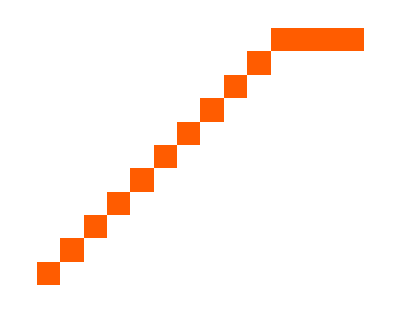

```mathematica
ArrayPlot[CellularAutomaton[{4, 4, 1}, {{1, 1, 1, 1}, 0}, 10], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]
```

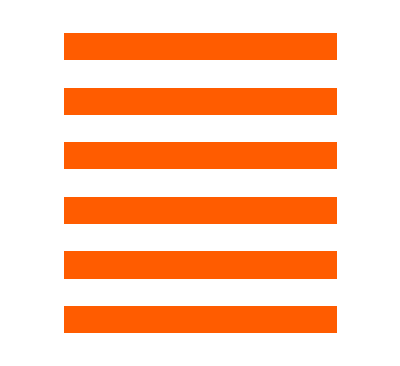
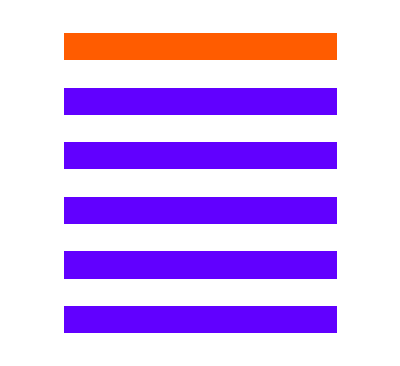
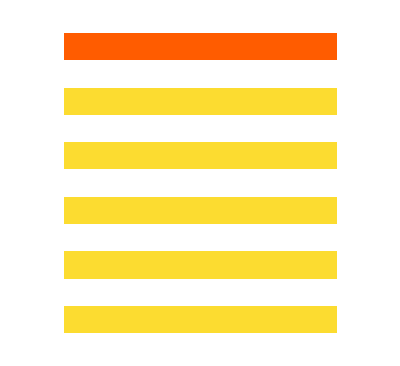
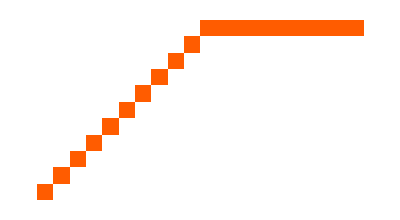
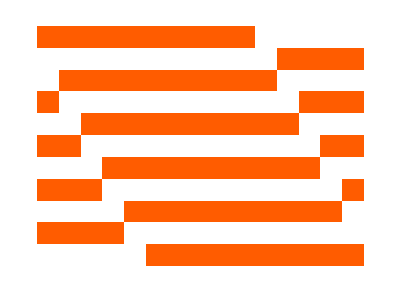
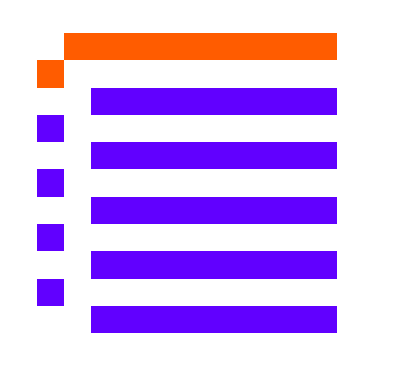
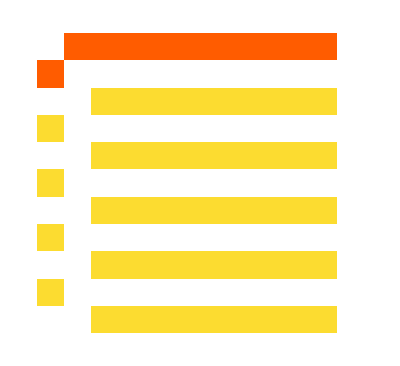
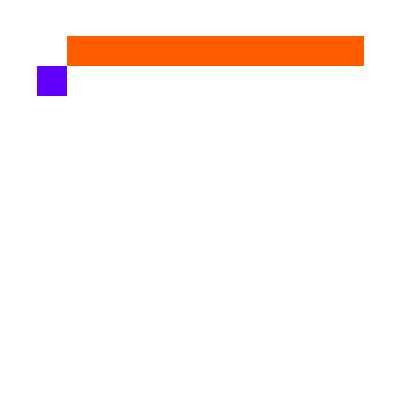
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ArrayPlot[CellularAutomaton[{i, 4, 1}, {Table[1, 10], 0}, 10], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]], {i, 1, 30}]
```

```mathematica
Row[With[{ru={299459058088077823758143088095350287424,4,1},pt=<|{15,206}->0|>},{{{"[◼]", "PlotCA"}}[ru,"Steps"->24,ImageSize->{Automatic,200},Mesh->All,MeshStyle->Opacity[.1]],{{"[◼]", "PlotCA"}}[ru,"Steps"->105,ImageSize->{Automatic,450},Mesh->All,MeshStyle->Opacity[.1]],Spacer[20],{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{24,{-200,200}},pt],Mesh->All,MeshStyle->Opacity[.1],ImageSize->{Automatic,200}],{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{105,{-200,200}},pt],Mesh->All,MeshStyle->Opacity[.1],ImageSize->{Automatic,450}]}],Spacer[10],Alignment->Bottom]
```

```mathematica
pcas = With[{ru={299459058088077823758143088095350287424,4,1}},{{"[◼]", "PerturbedCellularAutomaton"}}[ru, {{1}, 0}, {400, {-30, 40}}, #]&/@ {{"[◼]", "allperts"}}[CellularAutomaton[ru, {{1}, 0}, {400, {-30, 40}}]]];
```

```mathematica
widths=If[Length[#]===0,0,Last[#]-First[#]+1]&[{{"[◼]", "nonzeroRange"}}[#]]&/@#&/@pcas[[All,1]];
```

```mathematica
width0=If[Length[#]===0,0,Last[#]-First[#]+1]&[{{"[◼]", "nonzeroRange"}}[#]]&/@{{"[◼]", "PerturbedCellularAutomaton"}}[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {400, {-30, 40}}, <||>];
```

```mathematica
GraphicsRow[Show[ListStepPlot[Pick[widths,widths[[#,25]]<12&&widths[[#,25]]!=0&/@Range[Length[pcas]]],PlotRange->#,PlotStyle->RGBColor[0.95, 0.627, 0.1425],AspectRatio->.4,Frame->True,FrameLabel->{"time","width"}],ListStepPlot[width0,PlotStyle->RGBColor[0.24, 0.6, 0.8]]]&/@{{{0,50},{0,30}},{{0,240},Automatic}}]
```

```mathematica
ResourceFunction["PerturbedCellularAutomaton"]
```

```mathematica
{{"[◼]", "nonzeroRange"}}[{0, 0, 1,1, 2, 0}]
```

{3,5}

```mathematica
AliveQ[row_]:= Module[{ridx = {{"[◼]", "nonzeroRange"}}[row], body}, 
body = row[[#]]&@@ridx;
Max[Length/@ Split[body]]>5]
```

```mathematica
RandomCellularAutomatonRule
```

```mathematica
RandomChoice[{0, 1, 2, 3}, {15 , 4^(2*1+1) - 1}]
```